# Réflexion sur un miroir plan mobile

## Le principe de Fermat dans le référentiel lié au miroir

```mathematica
D[(c(t1[x]+t2[x])), x]==D[(√(H^2+(d-x)^2)+√((H+v(t1+t2))^2+(d+x)^2)), x]/.(t1'[x]+t2'[x])->0
```

0==-(d-x)/(√(H^2+(d-x)^2))+(d+x)/(√((H+(t1+t2) v)^2+(d+x)^2))

```mathematica
(* Cette relation établit l'égalité des angles d'incidence et de réflexion dans le référentiel lié au miroir car elle équivaut à : (d-x)/(c Subscript[t, 1])=(d+x)/(c Subscript[t, 2]) *)
```

```mathematica
Eliminate[{c t1==√(H^2+(d-x)^2),c t2==√((H+v(t1+t2))^2+(d+x)^2),(d-x)/(c t1)==(d+x)/(c t2)},{t1,t2}]
```

c^2 d H^2 x+c d H v (-d+x) √(d^2+H^2-2 d x+x^2)-d^2 v^2 (d^2+H^2-2 d x+x^2)==0&&c≠0

```mathematica
Solve[c^2 d H^2 x+c d H v (-d+x) √(d^2+H^2-2 d x+x^2)-d^2 v^2 (d^2+H^2-2 d x+x^2)==0,x]        (* On calcule ensuite les extrema en ne retenant que la seule racine positive compatible : *)
```

```mathematica
{{x->(d v^2-√(c^2 H^2 v^2-H^2 v^4))/v^2},{x->(d v^2+√(c^2 H^2 v^2-H^2 v^4))/v^2},{x->(-d^3 v^2-√(c^2 d^4 H^2 v^2+c^2 d^2 H^4 v^2-d^4 H^2 v^4))/(c^2 H^2-d^2 v^2)},{x->(-d^3 v^2+√(c^2 d^4 H^2 v^2+c^2 d^2 H^4 v^2-d^4 H^2 v^4))/(c^2 H^2-d^2 v^2)}}
```

```mathematica
x[v_,d_,c_,H_]:=d v/c(v/c-H/d √((H/d)^2+1-v^2/c^2))/(v^2/c^2-H^2/d^2)
```

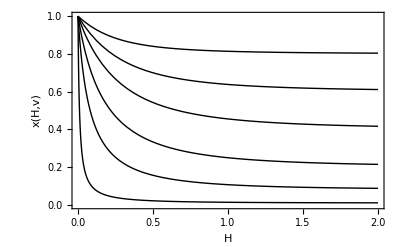

```mathematica
Plot[{x[0.01,1,1,H],x[0.08,1,1,H],x[0.2,1,1,H],x[0.4,1,1,H],x[0.6,1,1,H],x[0.8,1,1,H]},{H,0,2},PlotRange->{{0,2},{0,1}},Frame->True,PlotStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},PlotStyle->{Thick},LabelStyle->{Bold,Directive[14]},FrameLabel->{H,x[H,v]}]
```

## Le principe de Fermat dans le référentiel lié au couple source-détecteur

```mathematica
Solve[Numerator[Together[D[(H v/c+√(H^2+(d-x)^2)+√((H v/c+√(H^2+(d-x)^2))^2+4d x(1-v^2/c^2))), x]]]==0,x]
```

```mathematica
{{x->(d v^2-√(c^2 H^2 v^2-H^2 v^4))/v^2},{x->(d v^2+√(c^2 H^2 v^2-H^2 v^4))/v^2},{x->(-d^3 v^2-√(c^2 d^4 H^2 v^2+c^2 d^2 H^4 v^2-d^4 H^2 v^4))/(c^2 H^2-d^2 v^2)},{x->(-d^3 v^2+√(c^2 d^4 H^2 v^2+c^2 d^2 H^4 v^2-d^4 H^2 v^4))/(c^2 H^2-d^2 v^2)}}
```

## Note additionnelle

```mathematica
Series[√(Cos[θ]^2+(Sin[θ]-1/2)^2)+√(Cos[θ]^2+(Sin[θ]+1/2)^2),{θ,0,2}]
```

√5-(2 θ^2)/(5 √5)+O[θ]^3

```mathematica
Series[√((2-Cos[θ])^2+(Sin[θ]-1/2)^2)+√((2-Cos[θ])^2+(Sin[θ]+1/2)^2),{θ,0,2}]
```

√5+(18 θ^2)/(5 √5)+O[θ]^3

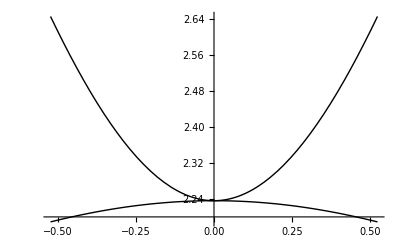

```mathematica
Plot[{√(Cos[θ]^2+(Sin[θ]-1/2)^2)+√(Cos[θ]^2+(Sin[θ]+1/2)^2),√((2-Cos[θ])^2+(Sin[θ]-1/2)^2)+√((2-Cos[θ])^2+(Sin[θ]+1/2)^2)},{θ,-π/6,+π/6},PlotStyle->{{Black,Thick},{Black,Thick}}]
```